# Willem Nielsen Work

### DONE: Very Clean and General Perturbation function, Vis function, Analysis functions, Wfr for Pert function,visualize changes in cells and lifetimes, single pertspec PerturbedCAEvolution function, PerturbedCAEvolution can take multiple coordinates at once, Different genes and phenotypes, Machine learning approach to finding medicine

### TODO: Adapting under perturbations, testing on different k-values, updating WFR for pert function, more thorough examination of behaviors of different rules, lifetime distribution plots for other rules, implement extract KR so it’s more like what SW wanted, try to speed up

## Functions

### Utility

```mathematica
FrontEndExecute[FrontEnd`AddMenuCommands["DuplicatePreviousOutput",{Delimiter,MenuItem["Delete cell",FrontEnd`KernelExecute[Module[{nb},nb=SelectedNotebook[];
SelectionMove[nb,Previous,Cell];
SelectionMove[nb,Next,Cell];
NotebookDelete[nb];
SelectionMove[nb,Next,Cell]]],MenuKey["k",Modifiers->{"Command"}],System`MenuEvaluator->Automatic]}]]
```

```mathematica
LocationDifferences[arr1_, arr2_, levelspec_:2] := Position[MapThread[{#1, #2} &, {arr1, arr2}, 2], {x_, y_} /; x != y, levelspec]
```

### Perturbation Viz

```mathematica
TrimArray[arr_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ arr,{}];
    If[ranges == {}, Return[arr]];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[Max[1, left-width] ;; Min[Length[arr[[1]]], right+width]]] & /@ arr,
    arr
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
ClearAll@PlotCA
```

```mathematica
Options[PlotCA] = {"init"->{{1}, 0}, "padding"->1, "steps"->{100, All}};
PlotCA[{ruleidx_Integer, k_Integer, r_Integer}, OptionsPattern[{ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},PlotDifferences, ArrayPlot, PlotCA}]] :=  
Module[
{steps = If[SameQ[OptionValue["steps"], Automatic], Max[{{"[◼]", "TestLifetime"}}[{ruleidx, k, r}, 200], 15], OptionValue["steps"]],ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ CellularAutomaton[{ruleidx, k, r}, OptionValue["init"], steps];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]
   ]]

PlotCA[ca_, OptionsPattern[{ColorRules -> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},PlotDifferences, ArrayPlot}]] :=
 ArrayPlot[TrimArray[ca, OptionValue["Trim"]], ColorRules -> OptionValue[ColorRules], 
 Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
```

```mathematica
ClearAll@PlotDifferences
```

```mathematica
Options[PlotDifferences] = {"Trim" -> {1, None}, MeshStyle -> Opacity[0.1], ColorRules -> Join[{0 -> White, -100 -> GrayLevel[.8]}, 
 {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :> Lighter[#2, .7] & @@@ {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
PlotDifferences[arr1_, arr2_, opsOptionsPattern[{PlotDifferences, ArrayPlot}]] := Module[{locs, vals, rus, highlighted, trimmed, colrules},
    locs = LocationDifferences[arr1, arr2];
    vals = arr2[[#1, #2]] & @@@ locs;
    rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
    highlighted = ReplacePart[arr1, rus];
    trimmed = TrimArray[highlighted, OptionValue["Trim"]];
    ArrayPlot[trimmed, ColorRules -> OptionValue[ColorRules], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
    ]
```

```mathematica
ClearAll@HighlightPerturbations
```

```mathematica
Options[HighlightPerturbations] = {ColorRules->Join[{100->Black},
    #1 -> GrayLevel[0.9] & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 -> #2& @@@ {0->GrayLevel[1],1->RGBColor[1, 0, 0],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
HighlightPerturbations[ca_, ops:OptionsPattern[{HighlightPerturbations, PlotDifferences, ArrayPlot}]]:= Module[{locs, rus, 
highlighted, trimmed},
locs = Position[ca, p[_, _]];
rus = ReplaceAll[#->-ca[[#[[1]], #[[2]], 2]]&/@ locs, 0:>100];
highlighted = ReplacePart[ca,rus];
trimmed = TrimArray[highlighted, OptionValue["Trim"]];
ArrayPlot[trimmed, ColorRules -> OptionValue[ColorRules], MeshStyle -> Opacity[0.1], ImageSize -> OptionValue[ImageSize]]
]
```

### Perturbation Function

```mathematica
p = Symbol["p"];
```

```mathematica
nonzeroRange[list_] := 
 Flatten[{FirstPosition[list, Except[0], Heads -> False],
  1 + Length[list] - FirstPosition[Reverse[list], Except[0], Heads -> False]}]
```

```mathematica
inrange[idxs_, range_ : {1}] := idxs[[Select[range, # >= -Length[idxs] && # <= Length[idxs] &]]]
```

```mathematica
tofunc[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  ((p[#, i] &) /@ # &),
   Rule["AddValue", i_Integer] :> ((p[#, Mod[(# + i), k]] &) /@ # &),
   "Random" :> ((p[#, RandomChoice[Complement[Range[0, k - 1], {#}]]] &) /@ # &),
   f_ :> f
   }]
```

```mathematica
expandrange[range_, n_] := ReplaceAll[
  Replace[range, 
   {(i_Integer) :> If[i >= 1, Range[i], Range[-1, i, -1]],
    List[i_Integer, o__] :> {If[i >= 1, Range[i], Range[-1, i, -1]], o}}],
  {All :> Range[n], {{s_Integer, e_Integer}} :> Range[s, e]}
  ]
```

```mathematica
tofullform[colspec_] :=
 Replace[colspec, {
   {js__Integer} :> {{js}, "Random", "Random"},
   {{js__Integer}, s_String} :> {{js}, s, "Random"},
   {{js__Integer}, s_String, f_} :> {{js}, s, f}}]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

```mathematica
MarkRowPerturbations[row_, colspec_, k_ : 3, r_ : 1] := Module[{coloridxs, range, 
order, bitfunc, sorted, incolorrange, pertbitfunc, vals},
  coloridxs = Replace[nonzeroRange[row], {{} :> {}, g_ :> Range @@ g}];
  {range, order, bitfunc} = tofullform[expandrange[colspec, Length[coloridxs]]];
  sorted = If[order === "Random", RandomSample[coloridxs, UpTo@Length[range]], coloridxs];
  incolorrange = sorted[[Select[range, # >= -Length[sorted] && # <= Length[sorted] &]]];
  pertbitfunc = tofunc[bitfunc, k];
  vals = pertbitfunc[row[[incolorrange]]];
  ReplacePart[row, MapThread[#1 -> #2 &, {incolorrange, vals}]]
  ]
```

```mathematica
MarkPerturbations[{ca_, {n_, k_, r_}}, pertspec_] := 
 {ReplacePart[ca, pertspec[[1]] -> MarkRowPerturbations[ca[[pertspec[[1]]]], pertspec[[2]], k, r]],
  {n, k, r}}
```

```mathematica
ClearAll@MarkPerturbationsByIndex
```

```mathematica
MarkPerturbationsByIndex[{ca_, {n_, k_, r_}}, {idxs_, pertbitfunc_}] := Module[{},
  {ReplacePart[ca, MapThread[#1 -> #2 &, {idxs, pertbitfunc[Flatten[ca[[#1, #2]] & @@@ idxs], k]}]], {n, k, r}}
  ]
```

```mathematica
ClearAll@EvolvePerturbedCA
```

```mathematica
EvolvePerturbedCA[{pca_, rule_}] := Module[{pidxs, pidx, prowidx, pre, prow, evolvedCA},
  pidxs = Position[pca, p[_, _], {}];
  If[pidxs == {}, {pca, rule},
   prowidx = pidxs[[1, 1]];
   pre = pca[[;; prowidx - 1]];
   prow = pca[[prowidx]] /. p[old_Integer, new_Integer] :> new;
   evolvedCA = Join[pre, CellularAutomaton[rule, prow, Length[pca] - Length[pre] - 1]];
       {evolvedCA, rule}
   ]]
```

```mathematica
ClearAll@PerturbIndexes
```

```mathematica
PerturbIndexes[{ca_, rule_}, idxspec_] := Module[{},
  {n, k, r} = interpretrule[rule];
  tolist = Replace[idxspec, {{i_Integer, j_Integer} :> {{i, j}}} ];
  {idxs, bitfuncspec} = If[ MatchQ[tolist, List[List[_Integer, _Integer] ..]],
   {idxspec, "Random"}, {First[idxspec], Last[idxspec]}];
  byrow = {#, tofunc[bitfuncspec, k]} & /@ GatherBy[SortBy[idxs, #[[1]] &], #[[1]] &];
  Fold[EvolvePerturbedCA[Sow[MarkPerturbationsByIndex[#1, #2]]] &, {ca, {n, k, r}}, byrow]
  ]
```

```mathematica
ClearAll@PerturbCA
```

```mathematica
PerturbCA[{ca_, rule_}, pertspec_ : "Random"] := Module[{rand, torand, tolist},
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, r_Rule :> {r}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, rule}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, rule}, tolist]][[1]]
  ]
```

```mathematica
PerturbCA[{n_Integer, k_Integer, r_?NumberQ}, init_:{{1}, 0}, steps_Integer:100, pertspec_ : "Random"] := Module[{ca, rand, torand, tolist},
  ca = CellularAutomaton[{n, k, r}, init, {steps, All}]; 
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  Echo[rand];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, ru_Rule :> {ru}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, {n, k, r}}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, {n, k, r}}, tolist]][[1]]
  ]
```

```mathematica
ClearAll@PerturbedCAEvolution
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_ : 100, pertspec_ : "Random"] := 
  Module[{ca = CellularAutomaton[rule, init, {steps, All}]},
  Replace[pertspec,
   {
    ("Random" | _Integer | _Rule | {_Integer, _Integer} | {_Rule ..} | {{_Integer, _Integer} .. } 
    | {{{_Integer, _Integer} ..  }, _Rule})
     :> EvolvePerturbedCA[Sow[PerturbCA[{ca, rule}, pertspec]]][[1]],
    ({{_Rule ..} ..} | {{{_Integer, _Integer} .. } ..} | {{{{_Integer, _Integer} ..  }, _Rule} ..}
     | {{{{_Integer, _Integer} ..  }, _Rule} ..})
      :> FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, #2]]] &, {ca, rule}, pertspec][[All, 1]],
    {{{{_Integer, _Integer} .. } ..}, r_Rule} :> 
    FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, {#2, r}]]] &, {ca, rule}, First[pertspec]][[All, 1]]
      }
        ]]
```

```mathematica
ClearAll@PerturbCA
```

#### WN Notes on Defining pertspec argument

```mathematica
MarkPerturbations[{ca_, rule_}, pertspec_]
```

```mathematica
PerturbCA[]
```

```mathematica
PerturbCAEvolution[]
```

```mathematica
x_->
```

```mathematica
x_-> {pertbitfunc, rangespec}
```

```mathematica
{{{x_, y_}..}, pertbitfunc}
```

```mathematica
-1-> xxx
```

Challenge is how to integrate rangespec with a user inputed rangespec. No the range spec needs to happen before hand. The func can choose to select only white though which would be nice. pertbitfunc

It would be nice to have the pertbitfunc do the rangespec as well, but if the user doesn’t want to have to specify that right? Well let’s think about how to make that work.

So imagine the user puts in something like towhite. But then the challenge would be how to determine where to apply it. Well maybe you do the ranging afterwards? But what’s the point of that, why not just do it forwards. Yea true.

Okay so there’s no way around the ranging, it has to work that way.

We have to rethink this because it should be able to handle negatives...what if in the case of an integer  we replace it with a span spec that is minimized and maximized within the range of a list. Okay let’s try it again.

We also have to think about how to deal this different row idxs right. So should this function take a list? I think it should because the alternative is to mark and return the ca, which makes no sense. For each rule or coordinate pair it should just return the idx? Well let’s think about that for a second.

We don’t actually want to allow for the mixing of rules with coords because then we’re doing the inefficient thing of applying pertbitfunc to a list of every single coordinate. You could get around this by just checking what exactly is in the list and responding accordingly

I’m thinking about whether to make pertbit func take a list of bits or  a single bit. It’s nice if it takes a list of bits because then you can just apply it to all the bits, but it’s annoying if you want to do a list of coordinates that aren’t in the same row. I’m just going to go with the single bit and take the heat if he calls me out on it. There’ll be no way to tell from his perspective

Idea: Enforce coords to be a list of list, probably going to want to do multiple coordinates at a time any way, so it won’t be much of  burden on the user. Also allows the user to do {10, 15} which means {10->1, 15->1}.

I actually am going to do the other way because, I feel like there are cases where you would want to do one coordinate and it’s not as bad to have to do 1s for multiple which

### Analysis Functions

```mathematica
ClearAll@CountDifferences
```

```mathematica
ClearAll[CountDifferences2]
```

```mathematica
CountDifferences[arr1_, arr2_, levelspec_:2]:= Count[arr1 - arr2, Except[0], levelspec]
CountSame[arr1_, arr2_, levelspec_:2]:= Count[arr1 - arr2, 0, levelspec]
```

```mathematica
CountSame[arr1_, arr2_]:=
```

```mathematica
TestCALifeTime[ca_]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

### PerturbedCAEvolution Options Syntax

```mathematica
row: {row->{"Random", {1}}}
row->jmax: {row->{"Random", Range[jmax]}}
row -> {j1, j2...}:  {row->{"Random", {j1, j2...}}}
row ->"Left": {row -> {"Left", 1}}
row ->{"Left", jmax}: {row->{"Left", Range[jmax]}}
{row->{"Order", {j1, j2...}}}
{10->1,15} : {10->1, 15->1}
{{10, 5}}: {{10, 5}}
{{10, {7, 8, 9, 10}}}
{10-> All}
{10, {{90, 100}}}
```

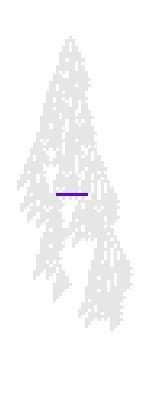

```mathematica
pca = Reap[PerturbCA[{initpat, ru}, 50->{"Center", {{1, 10}}}, toblue]][[2, 1, 1]];
HighlightPerturbations[pca]
```

#### SW Notes

```mathematica
{perspec,perbitfunc}
```

```mathematica
func[  {0,1,2,0,1,0,1,1,1,0}  ]
```

Pertbitfunc: 
“Random”
“SetValue” -> i
“AddValue” -> δ

Add value needs to be Mod

```mathematica
CellularAutomaton
```

```mathematica
extractKR[n_Integer]:={2,1}
```

```mathematica
extractKR[{_,k_Integer,r_Integer}]:={k,r}
```

## Running Code

### Init

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
ru = {5600111605818,3,1};
initpat = CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
ru ={5634850309665,3,1};
initpat = CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
ru ={264034764086666528641346401892089692680,4,1};
initpat = CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
ru ={rrules[[4]],3,1};
initpat = CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
rrules={4201857261303,4201857263490,4201857263409,4201856731968};
```

### Observing the effects of different therapies on different rules

#### Loading rules

```mathematica
evo = Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
];
```

```mathematica
evo[[All, 1]]
```

{{531441,3,1},{1558690240158,3,1},{514023487596,3,1},{4567913185281,3,1},{7287436131117,3,1},{5592884421399,3,1},{5586032021307,3,1},{5593005590109,3,1},{5624515853304,3,1},{5624518978527,3,1},{5634850309665,3,1},{5631363525264,3,1},{5599982465655,3,1},{5600111605818,3,1}}

```mathematica
evo2 = {{531441,3,1},{1558690240158,3,1},{514023487596,3,1},{4567913185281,3,1},{7287436131117,3,1},{5592884421399,3,1},{5586032021307,3,1},{5593005590109,3,1},{5624515853304,3,1},{5624518978527,3,1},{5634850309665,3,1},{5631363525264,3,1},{5599982465655,3,1},{5600111605818,3,1}};
```

```mathematica
evo3 = Module[
{goal=50,deep=5000,cut=200,ru,life,evo,data,res},
res=ParallelTable[CompoundExpression[
SeedRandom[745746+i],
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal]<=
Abs[Last[#]-goal],{ru,life},#]
]&,{{0,4,1},0},deep],
evo=Rest[First/@SplitBy[evo,Last]]],
{i,{2,12,14,21,31,38}}]
]
```

{{{{83076749738975093695720704310250496,4,1},1},{{305309519000392574664246621569920299136,4,1},2},{{142818508751749898935928745581588032136,4,1},6},{{142818568370942205086937694582740128392,4,1},7},{{63105128992655202831539910857546556040,4,1},8},{{987723115599443360580276856642119176,4,1},9},{{322975989919024744571721752855054917192,4,1},15},{{322975989919024744571720627163466587720,4,1},25},{{152814036320364080540621630254515510856,4,1},43},{{151484808324579164667717788009863082632,4,1},49},{{151484808364193245929459391025114534536,4,1},51},{{151463390144608385626127855126165607048,4,1},49},{{162159436740599612713704772333737628296,4,1},50}},{{{928455034075870758183109120,4,1},2},{{75106929167039989217338844733326219272,4,1},4},{{164594991695514537488502074254134585352,4,1},15},{{78859785967387482575672731819609917448,4,1},19},{{79524400005822476798720839348401439752,4,1},29},{{79524724523147866661034281870431599624,4,1},46},{{79524724523147828882102339748433214472,4,1},49},{{79524721987846666500587993270143924232,4,1},50}},{{{5566142232349335220090535082728620032,4,1},2},{{2705049293344874009315864354584642864,4,1},6},{{2705049293344874893606662786133116176,4,1},7},{{89021806214345109548507620625755261200,4,1},8},{{100984840429300873357499495899255916816,4,1},11},{{14395514544450819741125621628127922192,4,1},13},{{58280794599363678287128256961415477264,4,1},14},{{118721817511402735611818280188191438876,4,1},19},{{118721817516354495768671421360874977308,4,1},27},{{118742586703788639806199741031249868828,4,1},29},{{118738692481144729226906941664743389212,4,1},52},{{113421577673907819628396847532098975772,4,1},50}},{{{811296384372814195111928665210880,4,1},1},{{8980051707449673987924703928582144,4,1},3},{{175632210754459412266124055390314234256,4,1},5},{{128129755036507866602481259971004533136,4,1},12},{{53692987272552275488991856448032934288,4,1},14},{{53703429218793731854151107185289791888,4,1},21},{{53703429218793731798813122365932243344,4,1},31},{{53703425415841931112990015166698031504,4,1},44},{{53701153785966322421050438391278668176,4,1},54},{{53698517072717885482827187656017381776,4,1},53},{{53698517072563086014370819904606046608,4,1},51}},{{{41538374868278621028246169669665792,4,1},1},{{293433879771305571362681535866618718864,4,1},4},{{167821724688032113570647723898804306496,4,1},5},{{165417123015276382150865146876456801088,4,1},6},{{332540843951704215964948265516411650880,4,1},8},{{183667630407042456110875278020698571584,4,1},14},{{18761256646761174822966172619191747408,4,1},23},{{18720367308922841798325317099920687952,4,1},33},{{18720366992010172851802088023721116560,4,1},51},{{18720365724359573805317228731856225168,4,1},49}},{{{166155123650446026531896550320242688,4,1},1},{{32108692573706564099683950953431474304,4,1},5},{{243352913382588338036310504944264254860,4,1},10},{{329342561326403212300347242405729638028,4,1},40},{{329347751087960546671516072707164190348,4,1},49},{{329596982604821045373293092065478293132,4,1},51},{{329566069677264536515254482828731479692,4,1},50}}}

```mathematica
Module[{
k=3,r=1,cut=200,deep=5000,fun=Length,
init,evo,ru,data,lt,test,mask,canonical,res},
res=ParallelTable[SeedRandom[seed];
init=FromDigits[Lookup[Association[Thread[Append[
Permutations[CenterArray[1,2r+1]],
CenterArray[0,2r+1]]->1]],{{"[◼]", "RuleTuples"}}[k,r],0],2];
init={0,{0,init},1,fun[{{1}}]};
evo=NestList[Function[item,
ru=First[{{"[◼]", "RandomRuleMutation"}}[{First[item],k,r}]];
data=CellularAutomaton[{ru,k,r},{{1},0},{cut,All}];
lt=If[SameQ[#,0],True,cut-#+1]&[
LengthWhile[Reverse[data],Total[#]==0&]];
If[TrueQ[lt],item,
test=fun[{{"[◼]", "MatrixCrop"}}[data]];
If[test<Last[item],item,
data=Union[Catenate[Partition[#,2r+1,1]&/@data]];
mask=Lookup[Association[Thread[data->1]],{{"[◼]", "RuleTuples"}}[k,r],0];
canonical=IntegerDigits[ru,k,k^(2r+1)];
canonical={FromDigits[canonical*mask,k],
FromDigits[mask,2]};
{ru,canonical,lt,test}
]]],init,deep];
evo=Map[Rest@*First,SplitBy[evo,#[[2]]&]];
evo=Map[DeleteDuplicates,SplitBy[evo,Last]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7}]]&,
evo,{2}];
Map[First,res]
,
{seed,5000+{16,73,54,60}}];
GraphicsColumn[
Map[GraphicsRow,res]
]
]
```

#### Defining Sickness

```mathematica
rus=evo2;
pats = CellularAutomaton[#, {{1}, 0}, {60, All}]&/@ rus;
```

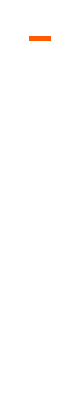
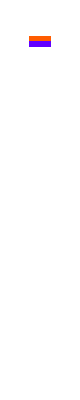
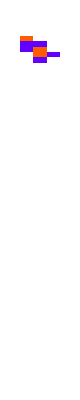
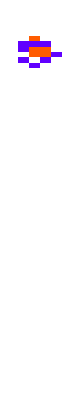
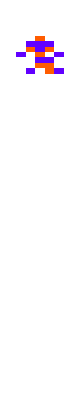
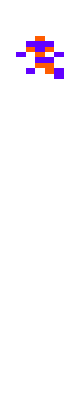
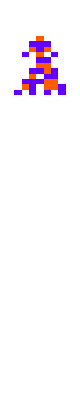
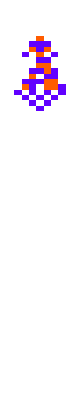

```mathematica
PlotCA/@ pats
```

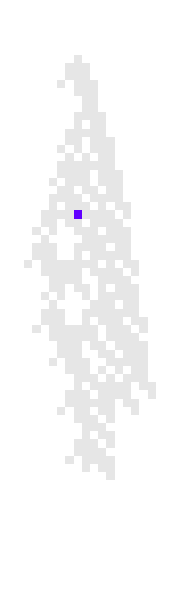
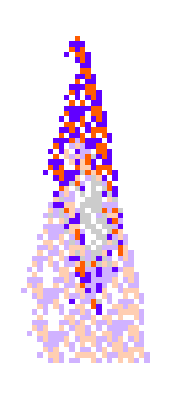
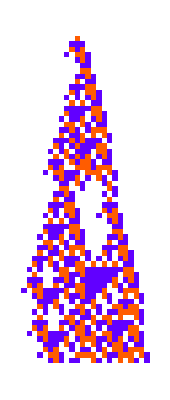
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
idx = -1;
pat = pats[[idx]]; ru = rus[[idx]];
loc = Reap[sick = PerturbCA[{pats[[-1]], rus[[-1]]}, 20]][[2, 1, 1, 1]];
{PlotCA[pats[[-1]]],HighlightPerturbations[loc, ImageSize->Small], PlotDifferences[pats[[-1]], sick[[1]]], PlotCA[sick[[1]]]}
```

Blue 20, 5 can be treated

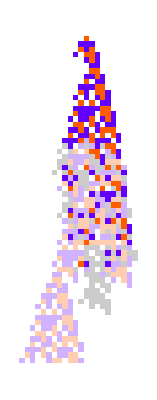
{-Graphics-,-Graphics-}

```mathematica
ri = RandomInteger[{1, 10000}];
SeedRandom[ri];
hp = Reap[ca = PerturbCA[{sick[[1]], ru}, 21->{{1, 5, 8}, "Enumerate", "SetValue"->0}]][[2, 1, 1, 1]];
{PlotDifferences[pat, PerturbCA[{sick[[1]], ru}, 21->{{1, 5, 8}, "Enumerate", "SetValue"->0}][[1]]], HighlightPerturbations[hp]}
```

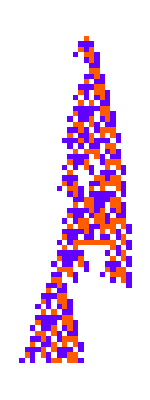

```mathematica
PlotCA[PerturbCA[{sick[[1]], ru}, 21->{{1, 5, 8}, "Enumerate", "SetValue"->0}][[1]]]
```

```mathematica
{PlotDifferences[pat, PerturbCA[{sick[[1]], ru}, 21->{{1, 5, 8}, "Enumerate", "SetValue"->0}][[1]]], HighlightPerturbations[locs[[pos[[2]]]]]}
```

{-Graphics-,-Graphics-}

#### Defining Treated

```mathematica
SeedRandom[4567];
locs = Table[Reap[PerturbCA[{sick[[1]], ru}, 21->3]][[2, 1, 1, 1]], 1000];
treated = Table[PerturbCA[{sick[[1]], ru}, 21->3], 1000];
```

#### Plotting Differences

```mathematica
(*rand11  = Table[{11, RandomInteger[{1, Length[initpat[[1]]]}]}, 10];*)
```

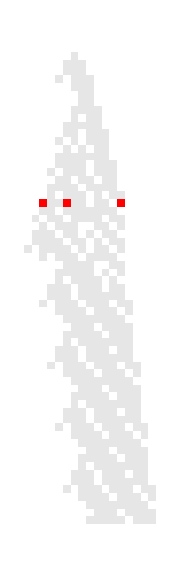
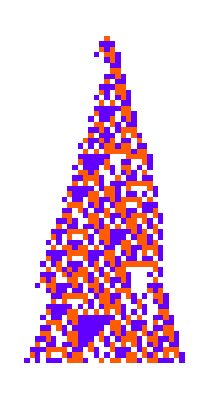
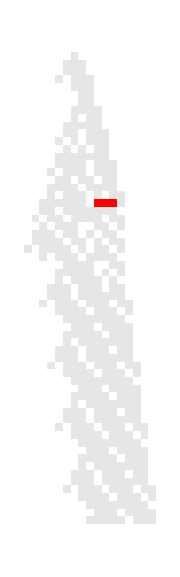
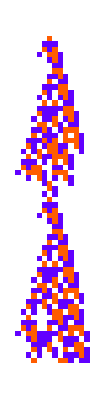
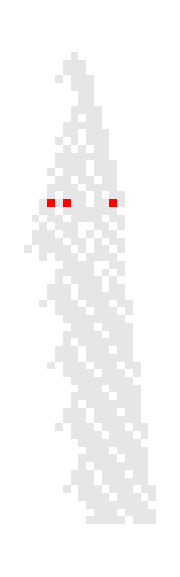
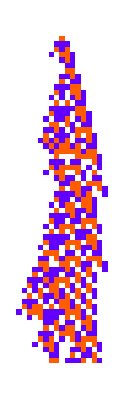
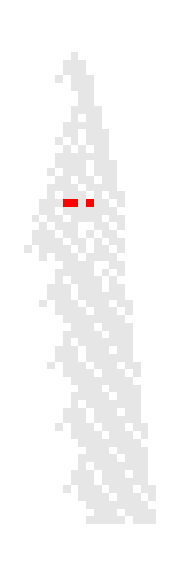
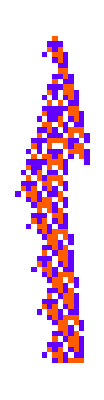
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
hps = HighlightPerturbations[#, ImageSize->Small]&/@locs[[2, 1, All, 1]];
ps = PlotCA[#]&/@ treated[[All, 1]];
hps = HighlightPerturbations[#, ImageSize->Small]&/@locs[[2, 1, All, 1]];
Transpose[{hps, ps}]
```

#### Analyzing Differences

```mathematica
initdiff = CountDifferences2[pat, sick[[1]]]
```

502

```mathematica
diffs = CountDifferences2[pat, #]&/@ treated[[All, 1]];
```

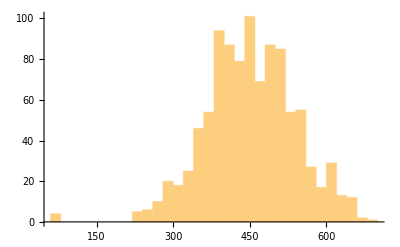

```mathematica
Histogram[diffs]
```

```mathematica
healed = Select[treated[[All, 1]], CountDifferences2[pat, #] <300&];
```

```mathematica
pos = Select[Range[Length[diffs]], diffs[[#]]<= 100&];
```

```mathematica
Length[pos]
```

4

```mathematica
treated[[pos[[2]], 1, 21]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,1,2,0,2,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

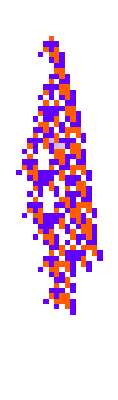
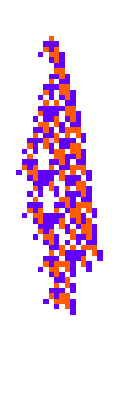
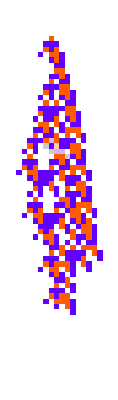
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[pat, #]&/@ treated[[All, 1]][[pos]]
```

```mathematica
pos
```

{659,745,762,903}

```mathematica
locs[[pos]]
```

```mathematica
locs[[745, 21]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,p[1,0],2,0,2,p[1,0],2,2,p[2,0],1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

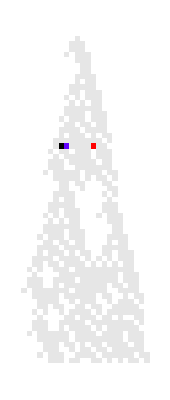
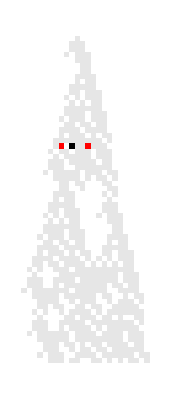
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightPerturbations/@ locs[[pos]]
```

```mathematica
CountDifferences[pat, treated[[All, 1]][[pos[[1]]]]]
```

2

```mathematica
treated[[All, 1]][[pos]]
```

```mathematica
PlotDifferences[pat,#]&/@  treated[[All, 1]][[pos]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Analyzing New Lifetime

```mathematica
TestCALifeTime[pat]
```

53

```mathematica
lts = TestCALifeTime/@ treated[[All, 1]];
```

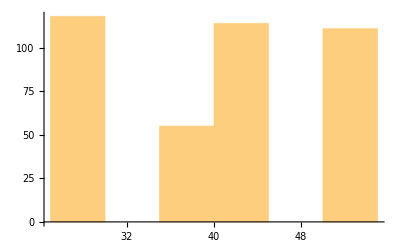

```mathematica
Histogram[lts]
```

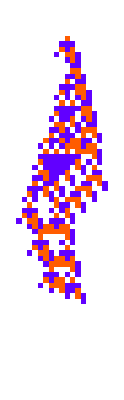
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Select[treated[[All, 1]], TestCALifeTime[#]<= 55 && TestCALifeTime[#]>= 50 &]
```

### Perturbing All Points on CA

```mathematica
nonzeroRange/@ initpat
```

{{101,101},{100,102},{100,102},{99,103},{99,103},{98,104},{98,104},{98,105},{98,104},{97,105},{97,105},{97,106},{96,106},{96,107},{95,106},{95,107},{95,106},{94,105},{94,105},{94,106},{94,105},{93,106},{93,106},{93,107},{93,107},{92,108},{92,107},{92,107},{92,108},{92,108},{91,109},{91,108},{91,108},{90,109},{90,108},{89,109},{89,109},{89,110},{88,110},{88,111},{87,111},{87,112},{87,111},{86,112},{86,112},{85,113},{85,113},{85,114},{88,114},{88,115},{87,115},{87,116},{86,115},{86,116},{86,115},{88,115},{88,116},{88,115},{91,114},{91,113},{94,114},{93,114},{93,115},{92,115},{92,116},{92,116},{92,117},{92,117},{91,118},{91,118},{91,119},{91,119},{91,120},{90,119},{90,120},{90,119},{97,119},{96,120},{96,119},{96,118},{96,117},{96,118},{96,117},{105,116},{105,117},{104,116},{104,117},{104,116},{106,117},{106,116},{106,115},{114,114},{},{},{},{},{},{},{},{},{}}

```mathematica
coloryidxs  = Range@@@(nonzeroRange/@ initpat[[;;Replace[TestCALifeTime[initpat], -Infinity:> Length[initpat]]-1]]);
coloridxs = Table[({i, #}&) /@ coloryidxs[[i]], {i, Length[coloryidxs]}];
```

```mathematica
Flatten[coloridxs, 1]  // Length
```

1772

```mathematica
allperts = PerturbCA[{initpat, ru}, #]&/@ Flatten[coloridxs, 1]
```

```mathematica
lts = TestCALifeTime/@ allperts[[All, 1]];
```

```mathematica
Histogram[lts]
```

-Graphics-

```mathematica
diffs = CountDifferences2[initpat,#]&/@ allperts[[All, 1]];
```

```mathematica
Histogram[diffs, PlotRange->{{0, 100}, Automatic}]
```

-Graphics-

### Testing Machine Learning Approach

#### Sickness

```mathematica
ri = RandomInteger[{1, 10000}];
RandomSeed[ri];
coloryidxs  = Range@@@(nonzeroRange/@ initpat[[;;Replace[TestCALifeTime[initpat], -Infinity:> Length[initpat]]-1]]);
coloridxs = Table[({i, #}&) /@ coloryidxs[[i]], {i, Length[coloryidxs]}];
marked = Reap[sick = PerturbCA[{initpat, ru}, 10]][[2, 1, 1, 1]];
{PlotCA[initpat],HighlightPerturbations[marked, ImageSize->Small], PlotDifferences[initpat, sick[[1]]], PlotCA[sick[[1]]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Mod[i, 1], {i, 10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
currdiff = CountDifferences[initpat, sick[[1]]];
ca = sick[[1]];
```

```mathematica
currdiff
```

873

```mathematica
AdaptTherapy[{initpat_, initru_}, {ca_, currdiff_, mca_, i_}]:= Block[{pca, nca, nmca, newdiff},
nmca = Reap[pca =PerturbCA[{ca, initru}, i]][[2, 1, 1, 1]];
newdiff = CountDifferences[initpat,pca[[1]]];
nca = If[newdiff< currdiff, pca[[1]],ca];
{nca, Min[newdiff, currdiff], nmca, If[Mod[i, 2]== 0, i + 1, i]}]
```

```mathematica
Histogram[Table[
e = NestList[AdaptTherapy[{initpat, ru}, #]& , {ca, currdiff, ca, 11}, 50];
m = Min[e[[All, 2]]], 50]]
```

-Graphics-

```mathematica
PlotCA/@ e[[All, 1]]
```

### Testing Perturbed Mean Adaptive Evolution

#### k = 3

```mathematica
evo3=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {100, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}][[1]], 1];
(*fitness = Min[ReplaceAll[Join[{TestCALifeTime[ca]}, TestCALifeTime/@ pcas], -Infinity:> 0]];*)
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,3,1},0},5000];
```

```mathematica
evo[[-1, 2]]
```

58

```mathematica
unique3 = DeleteDuplicatesBy[evo3[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

```mathematica
PlotCA[#,"steps"->100, "init"->{{1}, 0}]&/@ evo3[[-10;;, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbCA[{CellularAutomaton[evo3[[-1, 1]], {{1}, 0}, {100, All}], evo3[[-1, 1]]}][[1]]]
```

-Graphics-

```mathematica
{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicatesBy[evo[[All, 1]], {{"[◼]", "TestLifetime"}}],"Arrows"->"Line","MutationCounts"->True]
```

-Graphics-

#### Regular for comparison

```mathematica
evoreg3 = Module[
{deep=5000,cut=200,ru,life,evo,data},
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
];
```

```mathematica
PlotCA[#, "steps"->100, "init"->{{1}, 0}]&/@ evoreg3[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "RulesMutationPlot"}}[evoreg3[[All, 1]], "Arrows"->"Line","MutationCounts"->True]
```

-Graphics-

#### k = 4

```mathematica
evo4=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}][[1]], Ceiling[lt / 20]];
(*fitness = Min[ReplaceAll[Join[{TestCALifeTime[ca]}, TestCALifeTime/@ pcas], -Infinity:> 0]];*)
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},5000];
```

```mathematica
evo4[[-1, 2]]
```

112

```mathematica
unique = GatherBy[evo4[[All, 1]], {{"[◼]", "TestLifetime"}}][[All, -1]];
```

```mathematica
PlotCA[#,"steps"->200, "init"->{{1}, 0}]&/@ unique
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbCA[{CellularAutomaton[unique[[-1]], {{1}, 0}, {200, All}], unique[[-1]]}][[1]]]
```

-Graphics-

```mathematica
{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicatesBy[evo4[[All, 1]], {{"[◼]", "TestLifetime"}}],"Arrows"->"Line","MutationCounts"->True]
```

-Graphics-

#### Regular for comparison

```mathematica
evoreg4 = Module[
{deep=5000,cut=200,ru,life,evo,data},
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
];
```

```mathematica
PlotCA[#, "steps"->200, "init"->{{1}, 0}]&/@ evoreg4[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "RulesMutationPlot"}}[evoreg[[All, 1]], "Arrows"->"Line","MutationCounts"->True]
```

-Graphics-

### Observing Sickness Distribution on Normally Adapted Rules vs. Perturbed Rules

```mathematica
p4 = {{1080338744601344878852559786246963200,4,1},{176725032691429421183594526286552236800,4,1},{176766570749423735373793140793226560384,4,1},{243621641981010481257787093320256231564,4,1},{243869495562830144517314842719199717516,4,1},{243870793637044716538309792858541680780,4,1},{243869495562829780597641913567952005260,4,1},{243869493057239068186826503652189710476,4,1},{243859108463521998531569442401833232524,4,1},{243835743068237488811008733451783022732,4,1},{243835743068237488811008736750317906060,4,1},{243835743068237489991600357467729209484,4,1},{243835499679322246171555270100713777292,4,1},{243835499679322246171555270100713778316,4,1},{243835743083092770463023781535033371788,4,1},{243835743068237489991600357330290257036,4,1}};
```

```mathematica
Head[p4[[1, 1]]]
```

Integer

```mathematica
r4 = {{55340232221128654848,4,1},{229666748356335235007772364950122292268,4,1},{231001168648901314455849357456342541356,4,1},{335702556395462062557954974771479776796,4,1},{335702555130282355589290423474935238172,4,1},{165561371709262791498416800436335357468,4,1},{164226952684269941026113864376428736028,4,1},{249297701604571667736599372227014766108,4,1},{248633077465484084103234935260764909084,4,1},{248628858724286600113650480146820836892,4,1},{248630156798501233820557612770903137820,4,1},{78821280336978231057096260820089118236,4,1},{78821280336968559650539343786691468828,4,1},{78821280336659074640717998717966687772,4,1},{78821280336659074640717998717966425628,4,1}};
```

```mathematica
sickp4s = Table[Table[PerturbCA[{CellularAutomaton[p4[[i]], {{1}, 0}, {200, All}], p4[[i]]}][[1]], 100], {i,1, Length[p4]}];
```

```mathematica
sickr4s = Table[Table[PerturbCA[{CellularAutomaton[r4[[i]], {{1}, 0}, {200, All}], r4[[i]]}][[1]], 100], {i,1, Length[r4]}];
```

```mathematica
Map[Length, sickp4s[[All, All, All, 1]], {3}]
```

{{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}},{{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0},{401,0}}}

```mathematica
p4lts = Map[TestCALifeTime,sickp4s, {2}]
```

{{2,1,2,0,2,2,0,0,2,1,1,1,0,0,0,1,2,2,0,0,2,2,1,1,2,2,1,2,0,2,1,0,2,1,2,0,0,1,0,2,2,1,1,2,1,2,0,1,2,2,2,2,1,0,2,0,1,1,2,2,0,1,2,0,2,0,0,0,1,2,1,1,0,2,1,1,0,1,1,2,2,1,0,0,0,1,2,1,0,1,0,0,1,1,1,2,1,2,1,2},{2,2,0,2,5,0,0,2,1,2,1,2,2,4,2,4,0,1,2,1,0,5,4,4,2,2,4,4,4,0,1,5,5,0,2,4,2,2,2,0,4,1,2,0,4,2,0,1,1,2,1,1,1,1,4,2,1,4,1,1,2,2,1,2,1,5,1,1,4,5,4,5,2,4,4,2,2,1,2,0,1,2,2,1,1,1,2,2,5,4,5,4,2,2,1,2,2,2,2,4},{3,1,4,6,8,8,4,4,6,4,1,4,4,1,2,1,1,4,4,8,6,3,6,4,9,6,3,8,3,1,9,9,8,8,4,3,6,4,0,1,6,6,8,6,1,6,8,1,7,7,6,4,4,4,6,4,4,9,0,1,1,6,4,1,6,4,4,8,8,7,1,7,1,9,1,4,0,9,7,7,8,1,4,4,6,4,9,4,7,1,4,2,4,4,7,4,1,8,4,4},{1,-∞,8,2,8,2,8,2,7,10,8,3,9,11,9,1,5,5,10,3,8,1,1,11,10,7,5,3,5,1,2,8,5,5,1,9,5,8,-∞,8,10,5,3,9,5,0,9,5,5,7,8,2,0,4,8,5,2,5,1,3,1,10,9,2,1,9,1,10,0,4,2,4,5,3,8,5,6,7,11,5,10,-∞,9,4,8,7,8,4,-∞,0,8,1,5,5,8,2,2,10,1,5},{24,24,16,9,0,16,11,2,17,11,17,8,18,1,11,8,8,10,2,8,6,17,17,1,18,22,24,10,10,12,9,10,18,11,8,8,25,8,2,11,6,10,8,16,17,18,11,23,4,25,4,-∞,16,0,25,17,9,10,-∞,0,25,1,3,23,18,18,11,2,16,9,24,10,17,3,15,5,15,1,1,18,15,2,25,-∞,11,16,16,8,24,6,12,8,18,3,18,15,10,12,4,-∞},{15,23,42,-∞,31,25,43,-∞,34,5,18,25,39,24,36,26,40,28,-∞,47,6,28,26,-∞,24,42,30,24,40,34,46,10,36,18,22,44,20,27,30,26,24,26,6,31,-∞,33,41,31,42,41,8,38,36,32,13,26,37,-∞,45,29,38,3,29,12,39,43,8,33,25,28,17,21,31,38,30,42,1,8,31,33,27,37,26,30,45,26,6,42,-∞,42,-∞,42,-∞,17,32,43,38,47,30,29},{20,32,36,52,50,27,-∞,44,-∞,24,34,-∞,38,30,25,30,1,-∞,-∞,-∞,73,52,-∞,14,2,2,52,1,30,46,42,-∞,22,32,38,26,56,49,33,17,26,27,53,3,42,26,30,16,0,46,40,54,27,42,-∞,33,12,2,25,32,36,34,1,8,20,29,8,31,51,30,45,34,1,30,26,40,-∞,25,36,49,-∞,29,40,0,49,46,26,0,36,42,20,1,44,29,32,27,26,36,22,49},{30,33,32,3,50,18,40,51,32,26,24,3,51,28,32,26,32,46,22,26,46,24,56,32,27,2,46,1,49,34,51,12,50,49,43,42,27,54,50,41,52,43,51,24,30,42,29,34,28,44,53,0,46,54,41,22,50,46,51,26,32,55,31,12,53,10,48,31,44,22,24,50,54,35,22,45,52,55,34,36,19,28,35,32,43,39,54,38,8,44,10,18,30,48,52,13,27,0,27,9},{1,52,89,39,31,38,34,0,21,36,42,31,29,42,31,52,30,19,64,1,12,23,35,64,3,56,38,34,52,57,59,60,29,33,2,97,60,28,30,46,25,93,91,60,46,80,52,58,35,31,53,30,58,54,34,31,30,33,23,57,32,35,43,52,10,59,44,2,31,42,54,22,40,47,40,56,81,31,38,60,54,56,27,33,33,29,42,25,10,12,80,54,13,57,39,12,53,35,76,40},{60,-∞,40,-∞,48,43,68,41,-∞,42,2,62,40,67,39,38,44,15,62,62,8,1,57,-∞,-∞,68,68,15,44,29,82,36,39,-∞,58,68,62,-∞,-∞,48,81,71,10,99,-∞,39,53,60,76,77,75,39,65,13,-∞,40,-∞,72,74,3,-∞,82,51,68,-∞,35,40,54,0,44,-∞,38,76,74,10,39,88,68,24,38,-∞,37,21,62,-∞,2,69,24,65,50,24,50,70,59,-∞,48,62,-∞,25,30},{116,80,86,33,107,45,79,74,63,53,67,107,61,75,61,49,77,35,47,110,49,73,98,79,33,49,23,18,62,3,26,56,77,52,104,75,-∞,121,64,75,77,1,47,71,87,135,91,52,34,50,43,84,47,10,1,52,75,98,104,51,56,64,1,62,69,127,122,-∞,52,38,68,100,59,38,110,63,104,6,-∞,68,61,57,73,98,33,72,38,58,39,49,104,105,112,73,61,87,1,112,76,22},{85,63,62,53,90,61,39,53,52,70,53,49,59,45,92,33,18,59,52,52,13,36,106,59,72,1,54,65,108,16,51,1,82,92,117,85,82,54,92,106,20,43,34,50,50,36,8,66,61,35,92,86,39,71,10,53,32,32,61,52,50,67,36,56,61,30,98,61,51,54,53,60,124,29,122,37,60,92,57,56,102,116,105,27,73,20,81,65,124,78,39,71,45,39,75,101,22,66,117,99},{88,25,68,125,73,8,97,70,43,36,-∞,70,108,58,58,77,96,40,88,67,157,125,17,26,123,67,46,79,32,10,62,138,54,67,62,81,87,55,62,56,24,99,93,18,133,62,116,109,34,89,27,26,-∞,114,68,23,89,89,116,15,94,84,131,8,-∞,46,68,82,84,66,56,111,119,46,65,69,53,-∞,110,49,10,64,80,74,-∞,19,84,96,10,27,80,87,14,68,92,84,92,62,198,70},{82,150,20,92,78,129,124,2,138,152,129,82,113,114,172,135,145,77,29,32,92,145,51,18,139,134,84,31,167,178,78,42,101,134,82,130,152,59,155,101,163,121,103,32,163,150,178,150,129,87,84,62,116,68,118,1,151,104,143,78,167,54,1,84,142,129,83,44,28,49,161,123,162,134,84,72,133,82,13,163,84,52,160,125,1,95,80,72,20,133,88,150,131,102,63,37,111,175,43,155},{112,97,145,152,190,139,115,94,1,-∞,21,126,137,195,110,-∞,117,120,102,117,112,132,109,71,126,125,68,186,159,110,88,132,149,69,195,54,53,197,158,105,134,-∞,125,189,145,125,139,128,112,8,157,119,93,49,52,152,120,180,106,112,49,51,106,176,86,52,112,191,134,156,123,80,167,131,109,106,89,198,111,112,72,65,139,95,133,145,156,178,96,66,-∞,112,88,122,159,117,194,114,144,98},{61,102,-∞,150,115,-∞,89,176,130,154,106,140,132,65,-∞,64,1,91,-∞,143,48,85,153,121,81,21,84,136,71,137,99,101,88,75,95,127,141,166,79,102,-∞,40,145,124,80,169,108,166,113,150,151,65,113,-∞,52,163,129,68,-∞,165,151,91,151,89,92,86,186,89,175,167,35,127,49,147,-∞,84,-∞,118,85,142,112,65,86,103,149,30,-∞,143,158,112,30,129,40,157,159,6,83,-∞,130,109}}

```mathematica
r4lts =  Map[TestCALifeTime,sickr4s, {2}];
```

```mathematica
DistributionChart[p4lts]
```

-Graphics-

```mathematica
DistributionChart[p4lts/. -Infinity:> 0]
```

-Graphics-

```mathematica
DistributionChart[r4lts/. -Infinity:> 0]
```

-Graphics-

```mathematica
DistributionChart[r4lts]
```

-Graphics-

### Trying to measure robustness purely by rules

#### Loading rules

```mathematica
r3 = {{243,3,1},{43099452,3,1},{1547035732581,3,1},{1547021383728,3,1},{5059399803387,3,1},{5888273619138,3,1},{5877717492804,3,1},{5404766886996,3,1},{6252057149811,3,1},{2298172838289,3,1},{7099216678140,3,1},{4557479990136,3,1}};
```

```mathematica
p3 = {{0,3,1},{5083739628327,3,1},{4021750230972,3,1},{1097206670031,3,1},{4358593637385,3,1},{3492613237335,3,1},{4369243295067,3,1},{4651725444207,3,1},{4651725857550,3,1},{2109859970172,3,1},{1264895883825,3,1},{1169590443288,3,1},{1169619141102,3,1}};
```

```mathematica
p4 = {{1080338744601344878852559786246963200,4,1},{176725032691429421183594526286552236800,4,1},{176766570749423735373793140793226560384,4,1},{243621641981010481257787093320256231564,4,1},{243869495562830144517314842719199717516,4,1},{243870793637044716538309792858541680780,4,1},{243869495562829780597641913567952005260,4,1},{243869493057239068186826503652189710476,4,1},{243859108463521998531569442401833232524,4,1},{243835743068237488811008733451783022732,4,1},{243835743068237488811008736750317906060,4,1},{243835743068237489991600357467729209484,4,1},{243835499679322246171555270100713777292,4,1},{243835499679322246171555270100713778316,4,1},{243835743083092770463023781535033371788,4,1},{243835743068237489991600357330290257036,4,1}};
```

```mathematica
r4 = {{55340232221128654848,4,1},{229666748356335235007772364950122292268,4,1},{231001168648901314455849357456342541356,4,1},{335702556395462062557954974771479776796,4,1},{335702555130282355589290423474935238172,4,1},{165561371709262791498416800436335357468,4,1},{164226952684269941026113864376428736028,4,1},{249297701604571667736599372227014766108,4,1},{248633077465484084103234935260764909084,4,1},{248628858724286600113650480146820836892,4,1},{248630156798501233820557612770903137820,4,1},{78821280336978231057096260820089118236,4,1},{78821280336968559650539343786691468828,4,1},{78821280336659074640717998717966687772,4,1},{78821280336659074640717998717966425628,4,1}};
```

#### Running

```mathematica
EvolveAll[{pca_, rule_}] := Module[{pidxs, pidx, prowidx, pre, prow, evolvedCA},
  pidxs = Position[pca, p[_,_List], {}];
  If[pidxs == {}, {pca, rule},
   prowidx = pidxs[[1, 1]];
   pre = pca[[;; prowidx - 1]];
   prow = pca[[prowidx]] /. {i_Integer:> {i}, p[old_Integer, new_List] :> new};
allrows = Tuples[prow];
   evolvedCAs = Join[pre,CellularAutomaton[rule, #, Length[pca] - Length[pre] - 1]]&/@ allrows]
   ]
```

```mathematica
flipall[bits_, k_]:= ((p[#, Complement[Range[0, k - 1], {#}]] &) /@ bits)
```

```mathematica
getperts[tup_, k_]:= Tuples[Replace[ReplacePart[tup, Ceiling[Length[tup] / 2]->Complement[Range[0, k - 1], tup[[{Ceiling[Length[tup] / 2]}]]]], i_Integer:> {i}, 1]]
```

```mathematica
getpertrus[i_, perts_]:= i->#&/@ perts
```

```mathematica
getsubs[{n_, k_, r_}]:= MapThread[#1->#2&, {Tuples[Range[0, k - 1], 1 + 2r],IntegerDigits[n, k, 27]}]
```

```mathematica
getpertedges[k_, r_]:= getpertrus[#, getperts[#, k]]&/@Tuples[Range[0, k - 1],4r+ 1]
```

```mathematica
getruparts[arr1_->arr2_, r_:1]:= Transpose[Partition[#, 2r+1, 1]&/@ {arr1, arr2}]
```

```mathematica
pertdiffs[{n_, k_, r_}]:= Block[{ruparts, stepped},
 ruparts =Map[getruparts[#, r]&, getpertedges[ k, r], {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
totalpertdiffs[ru_]:= Total[pertdiffs[ru], 3]
```

```mathematica
UndirectedGraph[Catenate[getpertedges[3, 1]],EdgeStyle->Opacity[.4,White],VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->40, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}, GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

```mathematica
ListLinePlot[Table[totalpertdiffs[{RandomInteger[{1, 7625597484987}], 3, 1}], 500]]
```

-Graphics-

```mathematica
ug = UndirectedGraph[Map[getruparts[#, 2]&, getpertedges[ 2, 2], {2}]// Flatten[Map[#[[1]]->#[[2]]&,#, {3}]]& ,EdgeStyle->Opacity[.4,White],VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->30, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}]
```

-Graphics-

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
RuleTuples[k_,r_]:=RuleTuples[k,r]=Tuples[
Reverse[Range[0,k-1]],2r+1]
```

```mathematica
RuleMask[{ru_,k_,r_},lt_]:=Module[
{data,mask,canonical},
data=Union[Catenate[Map[Partition[#,2r+1,1]&,
CellularAutomaton[{ru,k,r},
CenterArray[1,2 r*(lt+4)+1],lt+2]]]];
mask=Lookup[Association[Thread[data->1]],RuleTuples[k,r],0]
(*canonical=IntegerDigits[ru,k,Length[mask]];{
FromDigits[canonical*mask,k],
FromDigits[mask,2]
}*)
]
```

```mathematica
ArrayPlot[RuleMask[#, TestLifetime[#, 200]]&/@ p4, Mesh->True]
```

-Graphics-

#### Viz to show connected rules after perturbation

```mathematica
pidxs, n, k, r
```

```mathematica
pts={{0,1},{2,5},{4, 1}};
```

```mathematica
CellularAutomaton[{n, k, r},
```

```mathematica
{n, k, r} = interpretrule[ru]
```

{6006804516645,3,1}

```mathematica
pca = MarkPerturbations[{initpat, ru}, 10->{{3}, "Enumerate", "SetValue"->2}][[1]]
```

```mathematica
pidxs = Position[pca, p[_,_], {}]
```

{{10,99}}

```mathematica
windows = pca[[#[[1]], #[[2]]- 2r;;#[[2]]+ 2r]]&/@ pidxs
```

{{2,2,p[1,2],1,2}}

```mathematica
oldwindows = # /. p[old_Integer, new_Integer]:> old&/@windows
```

{{2,2,1,1,2}}

```mathematica
newwindows = # /. p[old_Integer, new_Integer]:> new&/@windows
```

{{2,2,2,1,2}}

```mathematica
oldrulesets = Partition[#, 2r+1, 1]&/@ oldwindows
```

{{{2,2,1},{2,1,1},{1,1,2}}}

```mathematica
newrulesets = Partition[#, 2r+1, 1]&/@ newwindows
```

{{{2,2,2},{2,2,1},{2,1,2}}}

```mathematica
genepairs = MapThread[{#1, #2}&, {oldrulesets, newrulesets}, 2]
```

{{{{2,2,1},{2,2,2}},{{2,1,1},{2,2,1}},{{1,1,2},{2,1,2}}}}

```mathematica
locs = Map[getruleloc[#, k, r]&, genepairs, {3}]
```

{{{2,1},{5,2},{13,4}}}

```mathematica
getruleloc[bits_, k_, r_] :=  getruleloc[bits, k, r] = FirstPosition[RuleTuples[k, r], bits][[1]]
```

```mathematica
getgenelocs[{pca_, ru_}]:= Module[{}, 
{n, k, r} = interpretrule[ru];
pidxs = Position[pca, p[_,_], {}];
windows = pca[[#[[1]], #[[2]]- 2r;;#[[2]]+ 2r]]&/@ pidxs;oldwindows = # /. p[old_Integer, new_Integer]:> old&/@windows;newwindows = # /. p[old_Integer, new_Integer]:> new&/@windows;oldrulesets = Partition[#, 2r+1, 1]&/@ oldwindows;newrulesets = Partition[#, 2r+1, 1]&/@ newwindows;genepairs = MapThread[{#1, #2}&, {oldrulesets, newrulesets}, 2];locs = Map[getruleloc[#, k, r]&, genepairs, {3}] - 1/2
]
```

```mathematica
k^(2r+1)
```

27

```mathematica
windows
```

{{{{0,0,0,0,0,0,0,0,0,0,p[1,0],0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{243,3,1}}⟦1,-1;;3⟧}

```mathematica
getgenelocs[{pca, r3[[1]]}]
```

Part::take: Cannot take positions -1 through 3 in {{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},{0,0,0,0,0,0,0,0,0,0,«11»},«1»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

{{{-1/2+NotFound,-1/2+NotFound},{3/2,3/2},{-1/2+NotFound,-1/2+NotFound}}}

```mathematica
ImageSize->OptionValue[ImageSize],Mesh->OptionValue[Mesh], MeshStyle->OptionValue[MeshStyle], ColorRules->OptionValue[ColorRules]
```

```mathematica
ClearAll@plotrule
```

```mathematica
plotrule[rule_, ops:OptionsPattern[{"Trim"->{None, None}, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
PlotCA[{digits}, "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
plotmaskedrule[rule_, ops:OptionsPattern[{"Overlap"->False,"Trim"->{None, None}, ColorRules->withmask,Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
mult = If[OptionValue["Overlap"], -1, 100];
mask = RuleMask[rule, TestLifetime[ru]]*mult;
masked = (mask/. 0:> 1) * ReplaceAll[digits, 0:> 100];
PlotCA[If[OptionValue["Overlap"], {masked}, {digits, mask}], "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
mas
```

If inactive lighter, if white inactive gray

```mathematica
overlaplightrules = Join[{-100 -> GrayLevel[.8]}, 
   #1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

If active lighter, if white active gray

```mathematica
overlapdarkrules =  Join[{100 -> GrayLevel[.5]}, 
   -#1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    #1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

```mathematica
withmask ={0->GrayLevel[1], 1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 100->GrayLevel[0.2]};
```

```mathematica
plotmaskedrule[r3[[5]],ColorRules-> withmask]
```

-Graphics-

```mathematica
locs = getgenelocs[{pca, ru}]
```

{{{3/2,1/2},{9/2,3/2},{25/2,7/2}}}

```mathematica
getmidx[x1_, x2_]:= (x1 - x2)/ 2+x2
```

```mathematica
withmid = {#[[1]], #[[1]] - }
```

{{{{2,2},{1,2}},{{5,2},{2,2}},{{13,2},{4,2}}}}

```mathematica
withmid = Map[{#[[1]], getmidx[#[[1]], #[[2]]], #[[2]]}&, locs, {2}]
```

{{{3/2,1,1/2},{9/2,3,3/2},{25/2,8,7/2}}}

```mathematica
pts = Map[{{#[[1]], 1}, {#[[2]],4}, {#[[3]], 1}} &, withmid, {2}]
```

{{{{3/2,1},{1,4},{1/2,1}},{{9/2,1},{3,4},{3/2,1}},{{25/2,1},{8,4},{7/2,1}}}}

```mathematica
curves = Map[BezierCurve, pts, {2} ]
```

{{BezierCurve[{{3/2,1},{1,4},{1/2,1}}],BezierCurve[{{9/2,1},{3,4},{3/2,1}}],BezierCurve[{{25/2,1},{8,4},{7/2,1}}]}}

```mathematica
witharrows = Arrow/@ Flatten[curves]
```

{Arrow[BezierCurve[{{3/2,1},{1,4},{1/2,1}}]],Arrow[BezierCurve[{{9/2,1},{3,4},{3/2,1}}]],Arrow[BezierCurve[{{25/2,1},{8,4},{7/2,1}}]]}

```mathematica
g = Graphics[{Arrowheads[0.035],White, witharrows}]
```

```mathematica
ClearAll@getcurves
```

```mathematica
getcurves[locs_, y_:2]:= Module[{},
withmid = Map[{#[[1]], getmidx[#[[1]], #[[2]]], #[[2]]}&, locs, {2}];
pts = Map[{{#[[1]], y}, {#[[2]],y+2}, {#[[3]], y}} &, withmid, {2}];
curves = Map[BezierCurve, pts, {2} ];
witharrows = Arrow/@ Flatten[curves];
Graphics[{Arrowheads[0.025],White, witharrows}]
]
```

```mathematica
PlotCA[r3[[2]]]
```

-Graphics-

```mathematica
ca = CellularAutomaton[r3[[1]], {{1}, 0}, {10, All}]
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
pca = MarkPerturbations[{ca, r3[[1]]}, 1->1][[1]]
```

{{0,0,0,0,0,0,0,0,0,0,p[1,0],0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
getgenelocs[{pca, r3[[1]]}]
```

{{{51/2,53/2},{47/2,53/2},{35/2,53/2}}}

```mathematica
PerturbedRulePlot[{pca_, ru_}]:= Show[plotmaskedrule[ru],getcurves[getgenelocs[{pca, ru} ]]]
```

```mathematica
PerturbedRulePlot[ MarkPerturbations[{CellularAutomaton[r3[[2]], {{1}, 0}, {10, All}], r3[[2]]}, 2->1]]
```

-Graphics-

```mathematica
MarkPerturbations[{CellularAutomaton[r3[[3]], {{1}, 0}, {10, All}], r3[[3]]}, RandomInteger[{1, TestLifetime[r3[[3]]]}]->1][[1]]
```

{{0,0,0,0,0,0,0,0,0,0,p[1,2],0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[r3[[i]], {{1}, 0}, {50, All}], r3[[i]]}, RandomInteger[{1, TestLifetime[r3[[i]]]}]->1]], {i, Length[r3]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Column@Table[PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[p3[[i]], {{1}, 0}, {100, All}], p3[[i]]}, RandomInteger[{1, TestLifetime[p3[[i]]]}]->1]], {i, Length[p3]}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
≥
```

-Graphics-

```mathematica
Show[plotmaskedrule[ru, ColorRules-> withmask]]
```

```mathematica
Show[g, plotrule[ru]]
```

-Graphics-

### Testing New MarkPerturbations

```mathematica
MarkPerturbationsByIndex[{initpat, ru}, {{10, 150}}]
```

### Distribution of Disease Impacts

#### 30, Random, 1

```mathematica
SeedRandom[120529];
ecas = Table[PerturbedCAEvolution[ru, {{1}, 0},  100, 30->1][[2, 1]], 1000];
```

Change in countdiffs

```mathematica
cds = CountDifferences[initpat, #]&/@ ecas;
```

```mathematica
Histogram[cds, PlotRange->All]
```

-Graphics-

#### Change in lifetime Random, Random, 1

```mathematica
SeedRandom[917623];
{eas, {pas}} = Reap[Table[PerturbedCAEvolution[ru, {{1}, 0},  200][[2, 1]], 1000]];
```

```mathematica
initlife = {{"[◼]", "TestLifetime"}}[ru];
newlts = TestCALifeTime/@ eas;
alive = DeleteCases[newlts, -Infinity];
Histogram[alive]
```

-Graphics-

```mathematica
ResourceFunction["SelectPositions"][{1, 2, 3}, #>= 1&]
```

{{1},{2},{3}}

```mathematica
similar = Flatten[ResourceFunction["SelectPositions"][eas, TestCALifeTime[#]<95 && TestCALifeTime[#]>90&]];
Length[similar]
```

105

```mathematica
HighlightPerturbations[pas[[#]]]&/@ similar[[;;50]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[initpat,# ]&/@ similar[[50;;70]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Change in lifetime more runs

```mathematica
SeedRandom[1222];
ecas3 = Table[PerturbedCAEvolution[ru, {{1}, 0},  200][[2, 1]], 10000];
```

```mathematica
Histogram[DeleteCases[TestCALifeTime/@ ecas3, -Infinity]]
```

-Graphics-

```mathematica
Length[DeleteCases[TestCALifeTime/@ ecas3, -Infinity]]
```

3663

### Distribution of Therapy Impacts

#### Initial disease

```mathematica
SeedRandom[1205];
pca = PerturbCA[{initpat, ru}, 10->1];
CountDifferences[initpat, pca[[1]]]
TestCALifeTime[pca[[1]]]
PlotDifferences[initpat, pca[[1]], ImageSize->Small]
```

1438

-∞

-Graphics-

#### Lifetime after treatment

Without deaths

```mathematica
SeedRandom[1111];
treated = Table[PerturbCA[pca, RandomInteger[{11 ,92}]-> 1], 10000];
evolved = EvolvePerturbedCA/@ treated;
(*HighlightPerturbations/@ treated[[;;10, 1]];*)
lts = TestCALifeTime/@ evolved[[All, 1]];
```

```mathematica
Histogram[lts]
```

-Graphics-

With deaths

```mathematica
Histogram[Replace[lts, -Infinity->0, 1]]
```

-Graphics-

#### Total Diffs

```mathematica
cds2 = CountDifferences[initpat, #]&/@evolved[[;;1000, 1]];
```

```mathematica
Histogram[cds2]
```

-Graphics-

```mathematica
alive2 = Select[evolved, TestCALifeTime[#[[1]]]!= -Infinity&];
```

```mathematica
Length[alive2]
```

1382

```mathematica
cds3 = CountDifferences[initpat, #]&/@alive2[[All, 1]];
```

Only alive diffs

```mathematica
Histogram[cds3]
```

-Graphics-

### Smaller Phenotype

```mathematica
ru2 = {5586032021307, 3, 1};
initpat2 =CellularAutomaton[ru2,{{1}, 0},{30,All}];
PlotCA[initpat2]
```

-Graphics-

```mathematica
SeedRandom[1125];
pcas = Table[PerturbedCAEvolution[ru2, {{1}, 0},30], 10];
PlotDifferences[initpat2, #]&/@ pcas
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Testing PerturbedCAEvolution

```mathematica
rands = Table[{{i, RandomInteger[{1, Length[initpat[[1]]]}]}}, {i, 11, 92}]
```

{{{11,125}},{{12,61}},{{13,41}},{{14,177}},{{15,24}},{{16,138}},{{17,134}},{{18,37}},{{19,115}},{{20,163}},{{21,162}},{{22,39}},{{23,39}},{{24,179}},{{25,18}},{{26,101}},{{27,111}},{{28,16}},{{29,140}},{{30,17}},{{31,65}},{{32,11}},{{33,60}},{{34,128}},{{35,110}},{{36,17}},{{37,13}},{{38,18}},{{39,82}},{{40,55}},{{41,53}},{{42,79}},{{43,112}},{{44,45}},{{45,44}},{{46,100}},{{47,81}},{{48,26}},{{49,120}},{{50,149}},{{51,188}},{{52,21}},{{53,26}},{{54,201}},{{55,5}},{{56,179}},{{57,116}},{{58,68}},{{59,15}},{{60,10}},{{61,116}},{{62,26}},{{63,96}},{{64,1}},{{65,21}},{{66,149}},{{67,14}},{{68,79}},{{69,28}},{{70,78}},{{71,2}},{{72,56}},{{73,99}},{{74,14}},{{75,181}},{{76,84}},{{77,174}},{{78,119}},{{79,144}},{{80,23}},{{81,49}},{{82,93}},{{83,50}},{{84,26}},{{85,13}},{{86,67}},{{87,12}},{{88,191}},{{89,94}},{{90,152}},{{91,161}},{{92,179}}}

```mathematica
evo = PerturbedCAEvolution[ru, {{1}, 0}, 100,{rands, "SetValue"->2}];
```

### Scratchpad

### Looking for differences in the ruleset of robust vs. fragile automata

```mathematica
RulePlot[CellularAutomaton[#], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&/@ r3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotrule/@ r3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotrule/@ p3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TestLifetime/@ p3
```

{2,3,4,6,7,8,10,13,16,21,23,25}

```mathematica
TestLifetime/@ r3
```

{1,2,3,4,5,6,7,9,15,22,23,31}

```mathematica
TestLifetime[#, 200]&/@ evoreg4[[All, 1]]
```

{1,2,15,18,27,31,32,36,37,74,124,135}

```mathematica
TestLifetime[#, 200]&/@ unique42
```

{1,2,6,9,11,13,15,17,24,18,19,20,21,30,33,34,42,56,80,81,77,92,107}

```mathematica
Column[plotrule[#, ImageSize->Medium]&/@ p4]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[plotrule[#, ImageSize->Medium]&/@ r4]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
RulePlot[CellularAutomaton[evoreg[[-1, 1]]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

-Graphics-

```mathematica
plotrule[evoreg[[-1, 1]]]
```

-Graphics-

```mathematica
plotrule[unique32[[-1]]]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[evoreg[[-1, 1]]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[unique32[[-1]]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

-Graphics-

```mathematica
lt2 = TestLifetime[unique32[[-1]]]
```

34

```mathematica
lt1 = TestLifetime[evoreg[[-1, 1]]]
```

37

```mathematica
RuleMask[evoreg[[-1, 1]],lt1]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
RuleMask[unique32[[-1]],lt2 ]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
{PlotCA[unique32[[-1]]], PlotCA[evoreg[[-1, 1]]]}
```

{-Graphics-,-Graphics-}

## SW Notes

#### How to store results of perturbations

```mathematica
{1,2,0,1,p[0,1],XXXX}
```

```mathematica
p[_,1]->XXX
```

```mathematica
PerturbedCAEvolution[   ]
```

```mathematica
PerturbationIndicatorFunction->
```

```mathematica
p[0,1]
```

```mathematica
{0,1}
```

```mathematica
Apply[p]
```

```mathematica
Last
```

```mathematica
-#[[2]]&
```

```mathematica
<|0->XXX,1->2,2->0|>
```

#### How to specify perturbations

```mathematica
<|1->{{5,"Enumeration"}}|>
```

```mathematica
<|1->{{5,"Random"},{6,"Random"}}|>
```

```mathematica
<|1->{{5,f},{6,"Random"}}|>
```

```mathematica
5
```

```mathematica
{5,First}
```

```mathematica
Range[6]
```

{1,2,3,4,5,6}

```mathematica
Range[4,11]
```

{4,5,6,7,8,9,10,11}

```mathematica
First[ ]
```

```mathematica
Last[   ]
```

### Analysis functions

lifetime after perturbation   [ AKA fitness ]

number of cells that stay the same after perturbation

### ML for therapy

Fitness function is either (a) how many cells we can return to their original state, or (b) how close we can get the lifetime to the original